```mathematica
Subscript[H, 0]= 67.37; α= 0.99; β=0.69; Subscript[Ω, m0]=0.315; Subscript[Ω, Λ0]= 0.6847; Subscript[Ω, r0]=  3 10^(-4);
```

```mathematica
H[z_,A_,B_]:= √(H0^2 (Omo (1+z)^3+ Oro (1+z)^4+(2A-3B)/(2-2 A+3 B)Omo (1+z)^3+(A-2B)/(1-A+2 B)Oro (1+z)^4+ ( 1- (2 Omo)/(2-2 A+3 B)-  Oro/(1-A+2 B) ) (1+z)^((2 (-1+A))/B)))
```

```mathematica
H2[z_,A_,B_]:= H0^2 (Omo (1+z)^3+ Oro (1+z)^4+(2A-3B)/(2-2 A+3 B)Omo (1+z)^3+(A-2B)/(1-A+2 B)Oro (1+z)^4+ ( 1- (2 Omo)/(2-2 A+3 B)-  Oro/(1-A+2 B) ) (1+z)^((2 (-1+A))/B))
```

```mathematica
Subscript[ρ̃, Λ][z_,A_,B_]:= ((2A-3B)/(2-2 A+3 B)Omo (1+z)^3+(A-2B)/(1-A+2 B)Oro (1+z)^4+ ( 1- (2 Omo)/(2-2 A+3 B)-  Oro/(1-A+2 B) ) (1+z)^((2 (-1+A))/B))
```

```mathematica
DensityPlot[If[0≤ Subscript[ρ̃, Λ][Z,α,β] ,1,-1]/. {H0 -> Subscript[H, 0]*10^3 /(c) ,Z-> 10^14 ,Omo -> Subscript[Ω, m0],Oml -> Subscript[Ω, Λ0], Oro -> Subscript[Ω, r0]},{α,0,1},{β,0,1},FrameLabel->{"α","β"},PlotPoints->200,LabelStyle->Directive[Black,Bold,10],PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Signo de ρ_Λ(α,β, z=10^14)"],Below]]
```

General::munfl: 1/100000000000001^397998. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/100000000000001^3168. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/100000000000001^6336. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Subscript[ρ, c][z_,A_,B_]:=(1/H0^2) * H2[z,A,B] ;  Subscript[Ω, r][z_,A_,B_]:= (Oro (1+z)^4 )/Subscript[ρ, c][z,A,B];
```

```mathematica
NumberForm[Limit[Subscript[Ω, r][z,A,B]/. {H0 -> Subscript[H, 0]*10^3 /(c), A-> α, B->β , Omo -> Subscript[Ω, m0],Oml -> Subscript[Ω, Λ0], Oro -> Subscript[Ω, r0]},z-> 10^(14)],{7,7}]
```

1.0100000

```mathematica
DensityPlot[Abs[1-Limit[Subscript[Ω, r][z,α,β]/. {H0 -> Subscript[H, 0]*10^3 /(c), Omo -> Subscript[Ω, m0],Oml -> Subscript[Ω, Λ0], Oro -> Subscript[Ω, r0]},z-> 10^(14)]],{α,0,1},{β,0,1},LabelStyle->Directive[Black,Bold,10],PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"| 1-Ω_r(α,β, z=10^14) |"],Below],FrameLabel->{"α","β"},ColorFunction->"SunsetColors",PlotPoints->200]
```

General::munfl: 1/100000000000001^397998. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/100000000000001^3168. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/100000000000001^6336. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Reduce[{1-A+2 B==1, 0<=A<=1, 0<=B<=1},{A,B}]
0≤A≤1&&B==A/2
```

0≤A≤1&&B==A/2

0≤A≤1&&B==A/2

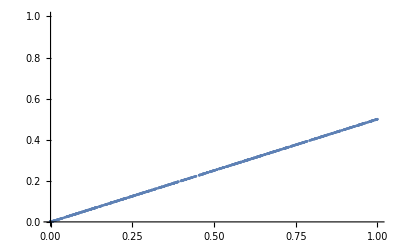

```mathematica
ListPlot[{A,B}/.N[FindInstance[{(1-10^(-4))≤1-A+2 B<1, 0≤A≤1, 0≤B≤1},{A,B},2*10^(3)]],PlotRange->{{0,1},{0,1}}]
```

```mathematica
Vs2[z_,A_,B_]:=(2 (2-2 A+3 B) (-2 (A-2 B) B^2 Oro (1+z)^(4+2/B)+(-1+A) ((-1+A-2 B) (-2+2 A-3 B+2 Omo)+(-2+2 A-3 B) Oro) (1+z)^((2 A)/B)))/(3 B (-2 (-1+A) ((-1+A-2 B) (-2+2 A-3 B+2 Omo)+(-2+2 A-3 B) Oro) (1+z)^((2 A)/B)+B (1+z)^(3+2/B) (-A (2+7 B) (3 Omo+4 Oro (1+z))+A^2 (6 Omo+8 Oro (1+z))+B (9 (1+2 B) Omo+8 (2+3 B) Oro (1+z)))))
```

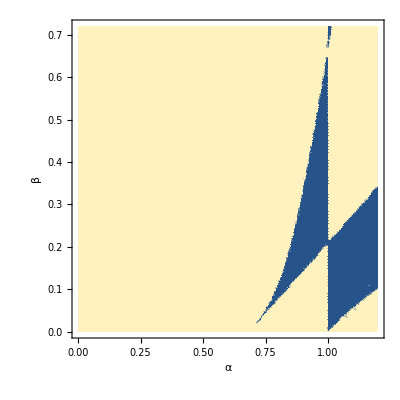

```mathematica
DensityPlot[If[0≤Vs2[Z,α,β]<1,0,1]/. { Z-> 0 ,Omo -> Subscript[Ω, m0],Oml -> Subscript[Ω, Λ0], Oro -> Subscript[Ω, r0]},{α,0,1.2},{β,0,0.72},LabelStyle->Directive[Black,Bold,10],PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"0 ≤ c_s^2(α,β, z=0) < 1  →  0 "],Below],FrameLabel->{"α","β"},PlotPoints->100]
```

```mathematica
q[z_,A_,B_]:= -1+((1+z) (3 Omo (1+z)^2+(3 (2 A-3 B) Omo (1+z)^2)/(2-2 A+3 B)+4 Oro (1+z)^3+(4 (A-2 B) Oro (1+z)^3)/(1-A+2 B)+(2 (-1+A) (1-(2 Omo)/(2-2 A+3 B)-Oro/(1-A+2 B)) (1+z)^(-1+(2 (-1+A))/B))/B))/(2 (Omo (1+z)^3+((2 A-3 B) Omo (1+z)^3)/(2-2 A+3 B)+Oro (1+z)^4+((A-2 B) Oro (1+z)^4)/(1-A+2 B)+(1-(2 Omo)/(2-2 A+3 B)-Oro/(1-A+2 B)) (1+z)^((2 (-1+A))/B)))
```

```mathematica
DensityPlot[If[0≥ q[Z,α,β],0,1]/. {H0 -> Subscript[H, 0] /(c) ,Z-> 0 ,Omo -> Subscript[Ω, m0],Oml -> Subscript[Ω, Λ0], Oro -> Subscript[Ω, r0]},{α,-2,2},{β,-2,2},FrameLabel->{"α","β"},PlotPoints->150]
```

-Graphics-

```mathematica
w[z_,A_,B_]:= ((-2+2 A-3 B) (-(A-2 B) B Oro (1+z)^(4+2/B)+((-1+A-2 B) (-2+2 A-3 B+2 Omo)+(-2+2 A-3 B) Oro) (1+z)^((2 A)/B)))/(3 B ((B (7+6 B-4 Omo-3 Oro)-2 (-1+Omo+Oro)) (1+z)^((2 A)/B)-B (1+z)^(3+2/B) ((3+6 B) Omo+2 (2+3 B) Oro (1+z))+2 A^2 ((1+z)^((2 A)/B)-(1+z)^(3+2/B) (Omo+Oro+Oro z))+A ((-7 B+2 (-2+Omo+Oro)) (1+z)^((2 A)/B)+(2+7 B) (1+z)^(3+2/B) (Omo+Oro+Oro z))))
```

```mathematica
DensityPlot[If[-1/3≥ w[Z,α,β],0,1]/. {H0 -> Subscript[H, 0] /(c) ,Z-> 0 ,Omo -> Subscript[Ω, m0],Oml -> Subscript[Ω, Λ0], Oro -> Subscript[Ω, r0]},{α,-2,2},{β,-2,2},FrameLabel->{"α","β"},PlotPoints->150]
```

-Graphics-

```mathematica
DensityPlot[If[0<=Vs2[Z,α,β]<1&& -1/3≥ w[Z,α,β] && 0 > q[Z,β,β] ,0,1]/. {H0 -> Subscript[H, 0]  ,Z-> 0 ,ZR-> 1,Omo -> Subscript[Ω, m0],Oml -> Subscript[Ω, Λ0], Oro -> Subscript[Ω, r0]},{α,0.1,1.2},{β,0.1,1.0},ImageSize->Large,LabelStyle->Directive[Black,Bold,10],Frame->True, FrameLabel->{{"β",""},{"α","Δ = 0"}},PlotPoints->200]
```

```mathematica
DensityPlot[If[0<=Vs2[Z,α,β]<1&& -1 ≤w[Z,α,β]&& 0<=Subscript[ρ̃, Λ][ZR,α,β] && 0.99≤1-α+2 β<1,0,1]/. {H0 -> Subscript[H, 0] /(c) ,Z-> 0 , ZR-> 10^(14),Omo -> Subscript[Ω, m0],Oml -> Subscript[Ω, Λ0], Oro -> Subscript[Ω, r0]},{α,0.8,1},{β,0.35,0.65},FrameLabel->{"α","β"},PlotPoints->450]
```

-Graphics-

```mathematica
ContourPlot[If[0<=Vs2[Z,α,β]<1&& -1 ≤w[Z,α,β]&& 0<=Subscript[ρ̃, Λ][ZR,α,β] && 0.9≤1-α+2 β≤1,0,1]/. {H0 -> Subscript[H, 0] /(c) ,Z-> 0 , ZR-> 10^(14),Omo -> Subscript[Ω, m0],Oml -> Subscript[Ω, Λ0], Oro -> Subscript[Ω, r0]},{α,0.8,1},{β,0.35,0.65},FrameLabel->{"α","β"},PlotPoints->450]
```

-Graphics-